```mathematica
<<JLink`
```

```mathematica
LoadJavaClass["java.awt.geom.Ellipse2D"];
```

```mathematica
LoadJavaClass["java.awt.geom.PathIterator"];
```

```mathematica
renderJavaShape[shape_]:=(
lastPoint=Null;
paths={};
coordsObj=JavaNew["[D",6];
pi=shape@getPathIterator[Null];
While[!pi@isDone[],
res=pi@currentSegment[coordsObj];
coords=JavaObjectToExpression[coordsObj];
Switch[res,
PathIterator`SEGUMOVETO,
Print[moveto];
lastPoint=coords[[1;;2]];
,
PathIterator`SEGUCLOSE,Print[close];,
PathIterator`SEGULINETO,
Print[lineto];
graphics=graphics~Append~Line[{lastPoint,coords[[1;;2]]}];
lastPoint=coords[[1;;2]]
,
PathIterator`SEGUQUADTO,Print[quadto];,
PathIterator`SEGUCUBICTO,
Print[cubicto];
graphics=graphics~Append~BezierCurve[{lastPoint}~Join~Partition[coords,2]];
lastPoint=coords[[5;;6]]
];
pi@next[]
];
graphics
)
```

moveto

cubicto

lineto

cubicto

close

moveto

cubicto

lineto

cubicto

cubicto

lineto

cubicto

lineto

cubicto

cubicto

lineto

cubicto

close

moveto

cubicto

cubicto

lineto

cubicto

cubicto

lineto

cubicto

cubicto

cubicto

lineto

cubicto

cubicto

cubicto

lineto

cubicto

cubicto

lineto

cubicto

cubicto

cubicto

lineto

cubicto

close

{BezierCurve[{{195.,128.179},{195.,128.179},{195.,128.179},{195.,128.179}}],Line[{{195.,128.179},{195.,128.179}}],BezierCurve[{{195.,128.179},{195.,128.179},{195.,128.179},{195.,128.179}}],BezierCurve[{{195.,171.821},{201.797,185.812},{214.928,196.158},{230.665,199.13}}],Line[{{230.665,199.13},{230.665,199.13}}],BezierCurve[{{230.665,199.13},{223.984,207.631},{220.,218.35},{220.,230.}}],BezierCurve[{{220.,230.},{220.,237.236},{221.537,244.112},{224.302,250.321}}],Line[{{224.302,250.321},{224.302,250.321}}],BezierCurve[{{224.302,250.321},{210.485,251.888},{198.376,259.087},{190.325,269.567}}],Line[{{190.325,269.567},{190.325,269.567}}],BezierCurve[{{190.325,269.567},{196.407,261.286},{200.,251.062},{200.,240.}}],BezierCurve[{{200.,240.},{200.,220.209},{188.501,203.104},{171.821,195.}}],Line[{{171.821,195.},{171.821,195.}}],BezierCurve[{{171.821,195.},{181.908,190.1},{190.1,181.908},{195.,171.821}}],BezierCurve[{{150.,100.},{122.386,100.},{100.,122.386},{100.,150.}}],BezierCurve[{{100.,150.},{100.,169.791},{111.499,186.896},{128.179,195.}}],Line[{{128.179,195.},{128.179,195.}}],BezierCurve[{{128.179,195.},{111.499,203.104},{100.,220.209},{100.,240.}}],BezierCurve[{{100.,240.},{100.,251.256},{103.719,261.643},{109.996,270.}}],Line[{{109.996,270.},{109.996,270.}}],BezierCurve[{{109.996,270.},{103.719,278.357},{100.,288.744},{100.,300.}}],BezierCurve[{{100.,300.},{100.,327.614},{122.386,350.},{150.,350.}}],BezierCurve[{{150.,350.},{166.356,350.},{180.878,342.147},{190.,330.005}}],Line[{{190.,330.005},{190.,330.005}}],BezierCurve[{{190.,330.005},{199.122,342.147},{213.644,350.},{230.,350.}}],BezierCurve[{{230.,350.},{257.614,350.},{280.,327.614},{280.,300.}}],BezierCurve[{{280.,300.},{280.,292.764},{278.463,285.888},{275.698,279.679}}],Line[{{275.698,279.679},{275.698,279.679}}],BezierCurve[{{275.698,279.679},{300.629,276.851},{320.,255.688},{320.,230.}}],BezierCurve[{{320.,230.},{320.,205.576},{302.488,185.242},{279.335,180.87}}],Line[{{279.335,180.87},{279.335,180.87}}],BezierCurve[{{279.335,180.87},{286.016,172.369},{290.,161.65},{290.,150.}}],BezierCurve[{{290.,150.},{290.,122.386},{267.614,100.},{240.,100.}}],BezierCurve[{{240.,100.},{220.209,100.},{203.104,111.499},{195.,128.179}}],Line[{{195.,128.179},{195.,128.179}}],BezierCurve[{{195.,128.179},{186.896,111.499},{169.791,100.},{150.,100.}}]}

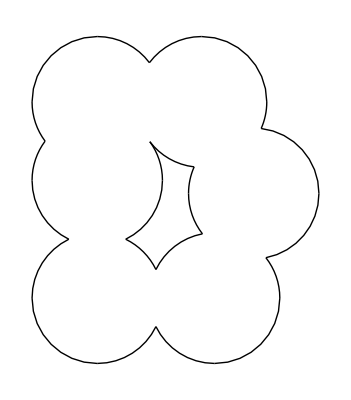

```mathematica
a=JavaNew["java.awt.geom.Area"];
a@add[JavaNew["java.awt.geom.Area",JavaNew["java.awt.geom.Ellipse2D$Double",100.0,100.0,100.0,100.0]]];
a@add[JavaNew["java.awt.geom.Area",JavaNew["java.awt.geom.Ellipse2D$Double",190.0,100.0,100.0,100.0]]];
a@add[JavaNew["java.awt.geom.Area",JavaNew["java.awt.geom.Ellipse2D$Double",220.0,180.0,100.0,100.0]]];
a@add[JavaNew["java.awt.geom.Area",JavaNew["java.awt.geom.Ellipse2D$Double",180.0,250.0,100.0,100.0]]];
a@add[JavaNew["java.awt.geom.Area",JavaNew["java.awt.geom.Ellipse2D$Double",100.0,250.0,100.0,100.0]]];
a@add[JavaNew["java.awt.geom.Area",JavaNew["java.awt.geom.Ellipse2D$Double",100.0,190.0,100.0,100.0]]];
renderJavaShape[a]
Graphics[%]
```

```mathematica
custom=JavaNew["java.awt.geom.GeneralPath"]
```

«JavaObject[java.awt.geom.GeneralPath]»

```mathematica
custom@moveTo[200,150]
```

```mathematica
custom@curveTo[200.,177.61423749153965,177.61423749153965,200.,150.,200.]
custom@curveTo[122.38576250846033,200.,100.,177.61423749153965,100.,150.]
custom@curveTo[100.,122.38576250846033,122.38576250846033,100.,150.,100.]
custom@curveTo[177.61423749153965,100.,200.,122.38576250846033,200.,150.]
```

```mathematica
custom@closePath[]
```

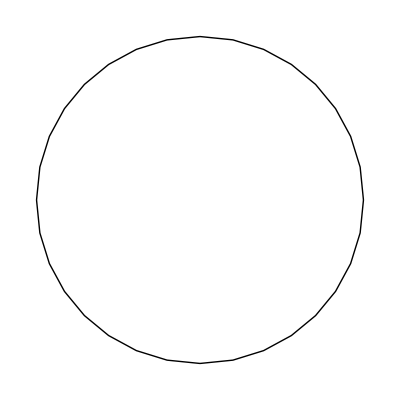

```mathematica
Graphics[renderJavaShape[custom]]
```

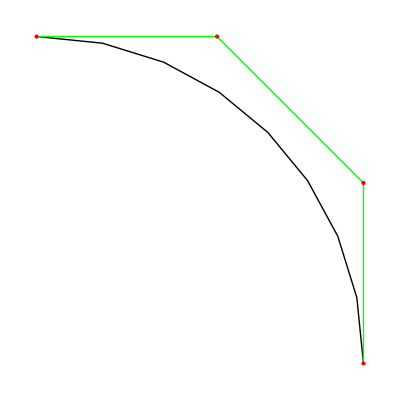

```mathematica
pts={{200,150},{200.,177.61423749153965},{177.61423749153965,200.},{150.,200.}};
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```